```mathematica
GetPlotRange::usage="GetPlotRange[gr] returns the actual unpadded plot range of graphics gr. GetPlotRange[gr, True] returns the actual padded plot range of gr. GetPlotRange can handle Graphics, Graphics3D and Graph objects.";
GetPlotRange[_[gr:(_Graphics|_Graphics3D|_Graph|_GeoGraphics),___],pad_]:=GetPlotRange[gr,pad];(*Handle Legended[…] and similar.*)GetPlotRange[gr_GeoGraphics,False]:=(PlotRange/.Quiet@AbsoluteOptions@gr);(*TODO:does not handle PlotRangePadding.*)GetPlotRange[gr_Graph,pad_: False]:=Charting`get2DPlotRange[gr,pad];
GetPlotRange[gr:(_Graphics|_Graphics3D),pad_: False]:=Module[{r=PlotRange/.Options@gr},If[MatrixQ[r,NumericQ],(*TODO:does not handle PlotRangePadding*)r,Last@Last@Reap@Rasterize[Show[gr,If[pad===False,PlotRangePadding->None,{}],Axes->True,Frame->False,Ticks->((Sow@{##};Automatic)&),DisplayFunction->Identity,ImageSize->0],ImageResolution->1]]];


(*Joins and filters options,keeping the righmost if there are multiple instances of the same option.*)
filter[opts_List,head_]:=Reverse@DeleteDuplicatesBy[Reverse@FilterRules[Flatten@opts,First/@Options@head],First];


(*Find and use SETools of Szabolcs& Halirutan*)
$SEToolsExist=FileExistsQ@FileNameJoin@{$UserBaseDirectory,"Applications","SETools","Java","SETools.jar"};

(*If SETools exist,initiate JLink and include some functions*)
If[$SEToolsExist,Needs@"JLink`";
JLink`InstallJava[];
copyToClipboard[text_]:=Module[{nb},nb=NotebookCreate[Visible->False];
NotebookWrite[nb,Cell[text,"Input"]];
SelectionMove[nb,All,Notebook];
FrontEndTokenExecute[nb,"Copy"];
NotebookClose@nb;];
uploadButtonAction[img_]:=uploadButtonAction[img,"![Mathematica graphics](",")"];
uploadButtonAction[img_,wrapStart_String,wrapEnd_String]:=Module[{url},Check[url=stackImage@img,Return[]];
copyToClipboard@(wrapStart<>url<>wrapEnd);];
stackImage::httperr="Server returned respose code: `1`";
stackImage::err="Server returner error: `1`";
stackImage::parseErr="Could not parse the answer of the server.";
stackImage[g_]:=Module[{url,client,method,data,partSource,part,entity,code,response,error,result,parseXMLOutput},parseXMLOutput[str_String]:=Block[{xml=ImportString[str,{"HTML","XMLObject"}],result},result=Cases[xml,XMLElement["script",_,res_]:>StringTrim[res],Infinity]/.{{s_String}}:>s;
If[result=!={}&&StringMatchQ[result,"window.parent"~~__],Flatten@StringCases[result,"window.parent."~~func__~~"("~~arg__~~");":>{StringMatchQ[func,"closeDialog"],StringTrim[arg,"\""]}],$Failed]];
parseXMLOutput[___]:=$Failed;
data=ExportString[g,"PNG"];
JLink`JavaBlock[JLink`LoadJavaClass["de.halirutan.se.tools.SEUploader",StaticsVisible->True];
response=Check[SEUploader`sendImage@ToCharacterCode@data,Return@$Failed]];
If[response===$Failed,Return@$Failed];
result=parseXMLOutput@response;
If[result=!=$Failed,If[TrueQ@First@result,Last@result,Message[stackImage::err,Last@result];$Failed],Message[stackImage::parseErr];$Failed]];];


GraphicsButton::usage="GraphicsButton[lbl, gr] represent a button that is labeled with lbl and offers functionality for the static graphics object gr. GraphicsButton[gr] uses a tiny version of gr as label.";
MenuItems::usage="MenuItems is an option for GraphicsButton that specifies additional label :> command pairs as a list to be included at the top of the action menu of GraphicsButton.";
Options[GraphicsButton]=DeleteDuplicatesBy[Flatten@{MenuItems->{},RasterSize->Automatic,ColorSpace->Automatic,ImageResolution->300,Options@ActionMenu},First];
GraphicsButton[expr_,opts:OptionsPattern[]]:=GraphicsButton[Pane[expr,ImageSize->Small,ImageSizeAction->"ShrinkToFit"],expr,opts];
GraphicsButton[lbl_,expr_,opts:OptionsPattern[]]:=Module[{head,save,items=OptionValue@MenuItems,rasterizeOpts,dir=$UserDocumentsDirectory,file=""},rasterizeOpts=filter[{Options@GraphicsButton,opts},Options@Rasterize];
save[format_]:=(file=SystemDialogInput["FileSave",FileNameJoin@{dir,"."<>ToLowerCase@format}];
If[file=!=$Failed&&file=!=$Canceled,dir=DirectoryName@file;
Quiet@Export[file,If[format==="NB",expr,Rasterize[expr,"Image",rasterizeOpts]],format]]);
head=Head@Unevaluated@expr;
ActionMenu[lbl,Flatten@{If[items=!={},items,Nothing],"Copy expression":>CopyToClipboard@expr,"Copy image":>CopyToClipboard@Rasterize@expr,"Copy high-res image":>CopyToClipboard@Rasterize[expr,"Image",rasterizeOpts],"Paste expression":>Paste@expr,"Paste image":>Paste@Rasterize@expr,"Paste high-res image":>Paste@Rasterize[expr,"Image",rasterizeOpts],Delimiter,"Save as notebook…":>save@"NB","Save as JPEG…":>save@"JPEG","Save as TIFF…":>save@"TIFF","Save as BMP…":>save@"BMP",Delimiter,Style["Upload image to StackExchange",If[$SEToolsExist,Black,Gray]]:>If[$SEToolsExist,uploadButtonAction@Rasterize@expr],"Open image in external application":>Module[{f=Export[FileNameJoin@{$TemporaryDirectory,"temp_img.tiff"},Rasterize@expr,"TIFF"]},If[StringQ@f&&FileExistsQ@f,SystemOpen@f]]},filter[{Options@GraphicsButton,opts,{Method->"Queued"}},Options@ActionMenu]]];


PlotExplorer::usage="PlotExplorer[plot] returns a manipulable version of plot. PlotExplorer can handle Graph and Graphics objects and plotting functions like Plot, LogPlot, ListPlot, DensityPlot, Streamplot, etc. PlotExplorer allows the modification of the plot range, image size and aspect ratio. If the supplied argument is a full specification of a plotting function holding its first argument (e.g. Plot) the result offers functionality to replot the function to the modified plot range. PlotExplorer has attribute HoldFirst.";
AppearanceFunction::usage="AppearanceFunction is an option for PlotExplorer that specifies the appearance function of the menu button. Use Automatic for the default appearance, Identity to display a classic button or None to omit the menu button.";
MenuPosition::usage="MenuPosition is an option for PlotExplorer that specifies the position of the (upper right corner of the) menu button within the graphics object.";
Attributes[PlotExplorer]={HoldFirst};
Options[PlotExplorer]={AppearanceFunction->(Mouseover[Invisible@#,#]&@Framed[#,Background->GrayLevel[.5,.5],RoundingRadius->5,FrameStyle->None,Alignment->{Center,Center},BaseStyle->{FontFamily->"Helvetica"}]&),MenuPosition->Scaled@{1,1}};
PlotExplorer[expr_,rangeArg_: Automatic,sizeArg_: Automatic,ratioArg_: Automatic,opts:OptionsPattern[]]:=Module[{plot=expr,held=Hold@expr,head,holdQ=True,legQ=False,appearance,position,$1Dplots=Plot|LogPlot|LogLinearPlot|LogLogPlot,$2Dplots=DensityPlot|ContourPlot|RegionPlot|StreamPlot|StreamDensityPlot|VectorPlot|VectorDensityPlot|LineIntegralConvolutionPlot|GeoGraphics},head=held[[1,0]];
If[head===Symbol,holdQ=False;head=Head@expr];
If[head===Legended,legQ=True;
If[holdQ,held=held/.Legended[x_,___]:>x;
head=held[[1,0]],head=Head@First@expr]];
holdQ=holdQ&&MatchQ[head,$1Dplots|$2Dplots];
If[!holdQ,legQ=Head@expr===Legended;
head=If[legQ,Head@First@expr,Head@expr]];
If[Not@MatchQ[head,$1Dplots|$2Dplots|Graphics|Graph],expr,DynamicModule[{dyn,gr,leg,replot,rescale,new,mid,len,min=0.1,f={1,1},set,d,epilog,over=False,defRange,range,size,ratio,pt1,pt1sc=None,pt2=None,pt2sc=None,rect,button},{gr,leg}=If[legQ,List@@plot,{plot,None}];
size=If[sizeArg===Automatic,Rasterize[gr,"RasterSize"],Setting@sizeArg];
defRange=If[rangeArg===Automatic,GetPlotRange[gr,False],Setting@rangeArg];
ratio=If[ratioArg===Automatic,Divide@@Reverse@size,Setting@ratioArg];
epilog=Epilog/.Quiet@AbsoluteOptions@plot;
gr=plot;
(*When r1 or r2 is e.g.{1,1} (scale region has zero width),EuclideanDistance by defult returns Infinity which is fine.*)d[p1_,p2_,{r1_,r2_}]:=Quiet@N@EuclideanDistance[Rescale[p1,r1],Rescale[p2,r2]];
set[r_]:=(range=new=r;mid=Mean/@range;
len=Abs[Subtract@@@range];pt1=None;rect={};);
set@defRange;
(*Replace plot range or insert if nonexistent*)replot[h_,hold_,r_]:=Module[{temp},ReleaseHold@Switch[h,$1Dplots,temp=ReplacePart[hold,{{1,2,2}->r[[1,1]],{1,2,3}->r[[1,2]]}];
If[MemberQ[temp,PlotRange,Infinity],temp/.{_[PlotRange,_]->(PlotRange->r)},Insert[temp,PlotRange->r,{1,-1}]],$2Dplots,temp=ReplacePart[hold,{{1,2,2}->r[[1,1]],{1,2,3}->r[[1,2]],{1,3,2}->r[[2,1]],{1,3,3}->r[[2,2]]}];
If[MemberQ[temp,PlotRange,Infinity],temp/.{_[PlotRange,_]->(PlotRange->r)},Insert[temp,PlotRange->r,{1,-1}]],_,hold]];
rescale[h_,hold_,sc_]:=ReleaseHold@Switch[h,$1Dplots|$2Dplots,If[MemberQ[hold,ScalingFunctions,Infinity],hold/.{_[ScalingFunctions,_]->(ScalingFunctions->sc)},Insert[hold,ScalingFunctions->sc,{1,-1}]],_,hold];
appearance=OptionValue@AppearanceFunction/.{Automatic:>(AppearanceFunction/.Options@PlotExplorer)};
position=OptionValue@MenuPosition/.Automatic->Scaled@{1,1};
(*Print@Column@{rangeArg,sizeArg,ratioArg,appearance,position};*)button=If[appearance===None,{},Inset[appearance@Dynamic@GraphicsButton["Menu",dyn,Appearance->If[appearance===Identity,Automatic,None],MenuItems->Flatten@{{Row@{"Copy PlotRange → ",TextForm/@range}:>(CopyToClipboard[PlotRange->range]),Row@{"Copy ImageSize → ",InputForm@size}:>(CopyToClipboard[ImageSize->size]),Row@{"Copy AspectRatio → ",InputForm@ratio}:>(CopyToClipboard[AspectRatio->ratio])},If[MatchQ[head,$1Dplots|$2Dplots],{Delimiter,"Replot at current PlotRange":>(gr=replot[head,held,range];),"Linear":>{gr=rescale[head,held,{Identity,Identity}];},"Log":>{gr=rescale[head,held,{Identity,"Log"}]},"LogLinear":>{gr=rescale[head,held,{"Log",Identity}]},"LogLog":>{gr=rescale[head,held,{"Log","Log"}]}},{}],Delimiter}],position,Scaled@{1,1},Background->None]];
Deploy@Pane[EventHandler[Dynamic[MouseAppearance[Show[(*`dyn` is kept as the original expression with only updating `range`,`size` and `ratio`.*)dyn=Show[gr,PlotRange->Dynamic@range,ImageSize->Dynamic@size,AspectRatio->Dynamic@ratio],Epilog->{epilog,button,{FaceForm@{Blue,Opacity@.1},EdgeForm@{Thin,Dotted,Opacity@.5},Dynamic@rect},{Dynamic@If[over&&CurrentValue@"AltKey"&&pt2=!=None,{Antialiasing->False,AbsoluteThickness@.25,GrayLevel[.5,.5],Dashing@{},InfiniteLine@{pt2,pt2+{1,0}},InfiniteLine@{pt2,pt2+{0,1}}},{}]}}],Which[over&&CurrentValue@"AltKey"&&pt2=!=None,Graphics@{Text[pt2,pt2,-{1.1,1},Background->GrayLevel[1,.7]]},CurrentValue@"ShiftKey","LinkHand",CurrentValue@"ControlKey","ZoomView",True,Automatic]],TrackedSymbols:>{gr}],{"MouseEntered":>(over=True),"MouseExited":>(over=False),"MouseMoved":>(pt2=MousePosition@"Graphics";),"MouseClicked":>(If[CurrentValue@"MouseClickCount"==2,set@defRange];),"MouseDown":>(pt1=MousePosition@"Graphics";
pt1sc=MousePosition@"GraphicsScaled";),"MouseUp":>(If[CurrentValue@"ControlKey"&&d[pt1,pt2,new]>min,range=Transpose@Sort@{pt1,pt2};];set@range;),"MouseDragged":>(pt2=MousePosition@"Graphics";
pt2sc=MousePosition@"GraphicsScaled";
Which[CurrentValue@"ShiftKey",pt2=MapThread[Rescale,{MousePosition@"GraphicsScaled",{{0,1},{0,1}},new}]-pt1;
range=new-pt2;,(*Panning*)CurrentValue@"ControlKey",rect=If[pt1===None||pt2===None,{},Rectangle[pt1,pt2]];,(*Zooming rectangle*)True,f=10^(pt1sc-pt2sc);
range=(mid+(1-f) (pt1-mid))+f/2 {-len,len}ᵀ(*Zofom on `pt1`*)])},PassEventsDown->True,PassEventsUp->True],Dynamic[size,(size=#;
If[CurrentValue@"ControlKey",ratio=Divide@@Reverse@#])&],AppearanceElements->"ResizeArea",ImageMargins->0,FrameMargins->0]]]];
```

```mathematica
primorialGen[n_]:= Times @@ Prime /@ Range[n]
```

```mathematica
{#, PrimePi[#]}& /@ (primorialGen /@ Range[10]) // TableForm
```

```mathematica
signPermutations[coeff__]:=DeleteDuplicates[ Times[{coeff}, #1]& /@ Tuples[{-1,1}, Length[{coeff}]]]
polyFromCoeffs[coeffs__] := Total @ MapIndexed[#1 x^(First[#2]-1)&,{coeffs, 1}]
polyFromRoots[roots__]:=Times@@(x-{roots})
polysRoots[polys_] := Values/@Flatten[Solve[#1 == 0, x]&/@polys]
polysMinMaxs[polys_]:= Flatten[#1/.Solve[D[#1, x] == 0, x]&/@polys]
withSignOpposites[vars_]:=Join[vars,-vars]
polysPlot[polys_, paddingRatio_:0.03] :=Module[{
minDom,maxDom,
minRange, maxRange
},
{minDom, maxDom}= MinMax[polysRoots[polys], Scaled[paddingRatio]];
{minRange, maxRange} = MinMax[polysMinMaxs[polys], Scaled[paddingRatio]];
PlotExplorer@Plot[polys, {x,minDom, maxDom},PlotRange->{minRange, maxRange},  PlotLegends->"Expressions"]
]
```

```mathematica
Remove["pieceWisePoly","reduceRootsToReals"]
pieceWisePoly[poly_:polyFromCoeffs[c0,c1,c2]]:=Piecewise[{{Evaluate[poly/.x->1/x],RealAbs[x]<1},{poly,RealAbs[x]≥1}}]
reduceRootsToReals[{}]={};
reduceRootsToReals[{},_]={};
reduceRootsToReals[roots_,pow_:1]:=Join[Prepend[pow]@*ReIm/@roots,reduceRootsToReals[-(Chop@*Times)@@@Subsets[Select[#,(Chop[Im[#]]≠ 0&) ],{2}],pow+1]]&[ roots]
plotInvertedPoly[polys_, paddingRatio_:0.03]:=Module[{
roots=reduceRootsToReals[Values[Flatten@NSolve[poly,x]]],
pwPoly = pieceWisePoly[poly],
minDom,maxDom,
minRange, maxRange
},
(*{minDom, maxDom}= MinMax[Echo[Abs/@roots], Scaled[paddingRatio]];
{minRange, maxRange} = MinMax[Echo[Abs/@polysMinMaxs[poly]],*)
{minDom, maxDom}= MinMax[roots[[All,2]], Scaled[paddingRatio]];
{minRange, maxRange} = MinMax[Abs/@polysMinMaxs[{poly}], Scaled[paddingRatio]];
PlotExplorer@Plot[{pwPoly,poly},{x,minDom-1, maxDom+2},  PlotLegends->"Expressions",Epilog->{PointSize[0.015],Point[roots[[All,2;;3]]]}]]
plotInvertedPoly[polyFromCoeffs[1,-3,0]]
```

```mathematica
Times@@(Total@Prepend[#, x]&/@signPermutations[y,z])//Expand
```

```mathematica
xr Exp[I xo] + yr Exp[I yo]//FullSimplify
```

```mathematica
polysPlot @ Evaluate[polyFromCoeffs @@@signPermutations[0.1,2,3]]
```

```mathematica
unityRootSum/@{{x1,x2,x3},{s1,s2,s3}}//Expand
```

```mathematica
{unityRootCoeffs[Times@@(unityRootSum/@#),3],#}&/@Tuples[Permutations[{s1, s2, s3}],{3}]
```

```mathematica
Riffle[{unityRootCoeffs[Times@@(unityRootSum/@#),3],#}&/@Tuples[Permutations[{s1, s2, s3}],{3}],"-------------------"]//Expand//TableForm
```

```mathematica
roots1 = signPermutations[3,2,-1]
polyAllRoots = polyFromRoots@@(DeleteDuplicates@Flatten@roots1)
p1=polyFromRoots@@@roots1
polysPlot @ Prepend[p1, polyAllRoots]
```

```mathematica
p1
```

```mathematica
sVars= -{s1,s2,s3}
oppSVars=withSignOpposites[sVars]
polys1 =polyFromRoots@@@{sVars, oppSVars}
coeffs1 =PadRight[CoefficientList[#, x],Length[oppSVars] + 1]&/@polys1
degs1 = Table[x^i,{i,0, Length[oppSVars]}]

TableForm[Transpose[Times[degs1, #]& /@coeffs1]]
polys1//Expand
(*polysPlot@polys1//Quiet*)
```

```mathematica
polysRoots[D[polyFromCoeffs[signPermutations[1,3,2,0.1]], x]]
polysMinMaxs[polyFromCoeffs[signPermutations[1,3,2,0.1]]]
D[polyFromCoeffs[signPermutations[1,3,2,0.1]], x]
Table[{#1, Total[#1]}& @ (CountRoots[#1, x] &/@ polyFromCoeffs[signPermutations[1,3,2,i]]), {i,0,5, 0.05}]//MatrixForm

CountRoots[#1, x]&/@Evaluate[polyFromCoeffs[signPermutations[1,3,2,4,0]]]
IreducPolyProduct[n_]:=Product[Total [{x,1} *(Symbol[# <> ToString[i]]&/@{"t", "s" }) ], {i,1,n}]
{Apply[List,Collect[IreducPolyProduct[3]//Expand, x]]}//Transpose//TableForm


((x-3)(x+2)(x-7))^(1/3)
```

```mathematica
(ruE[1,3](x-3)(x+2)(x-7))^(1/3)/.x->4//Expand//Simplify
```

```mathematica
DensityPlot[ReIm[(#-3)(#+2)(#-5)]&[(r1-d) ruE[1,3]+(r1+d) ruE[2,3]],{r1,-3, 50}, {d, -3,50}]
```

```mathematica
dimSqareRegionPred[s_, dim_, var_:t]:=((
var ≥ s
∧0 ≤ dim ≤ var-s
)∨(
var<s
∧0>dim≥var-s
))
rp1[s1_,s2_]:=With[{min=Min[s1,s2],max=Max[s1,s2]},
RegionPlot3D[dimSqareRegionPred[s1,y,x]∧dimSqareRegionPred[s2,z,x],{x,min-3,max+3},{y,min-s1-3,max+s1+8},{z,min-s2-3,max+s2+3},
AxesLabel->Automatic,PlotPoints->100, AxesOrigin->{0,0,0}, Boxed->False]]
```

```mathematica
rp1[-3,2]
```

```mathematica
Plot[{(*x-3,x+2,x-7,*) CubeRoot[((x-3)(x+2)(x-7))]Abs[CubeRoot[((x-3)(x+2)(x-7))]],CubeRoot[((x-3)(x+2)(x-7))],(x-3)(x+2)(x-7)},{x,-2.03,-1.97}]
PlotExplorer@Plot[{x-9,x+2, Re[(I+1) Sqrt[((x-9)(x+2))]],Re[(I+1) Sqrt[(I+1) Sqrt[((x-9)(x+2))]]],((x-9)(x+2))},{x,-3,10}, ImageSize->Large]
```

```mathematica
DiscretePlot3D[m^2-n^2,{m,0,First[#]},{n,0,Last[#]}, AxesLabel->Automatic,ExtentSize-> Full,PlotMarkers->{"Point",Large}]&@{5}
```

-Graphics3D-

## Unity Roots

```mathematica
Simplify[Complex[a,b],{a,b}∈Reals && a>0 &&b>0]
```

```mathematica
FullDefinition[ruE]
```

```mathematica
<<Notation`
(*RemoveSymbolize[ξ]
RemoveNotation[Subscript[ξ, n_]^k_ ⟺ ruE[k_,n_]]
RemoveNotation[Subscript[ξ, n_]^k_ ⟺ ruE[k_,n_]]*)
Notation[Subscript[ξ, n_]^k_ ⟺ ruE[k_,n_]]
```

```mathematica
ClearAll[ruE,ruETimes, ruEInit,ruEPlus,ruEMag]
SetAttributes[ruE,{Constant}]
ruE[0]=ruE[0,1];
ruE[0,_]=ruE[0,1];

(*ruEInit[0]=ruEInit[1] = False;
ruEInit[n_Integer]/;n>1:=(ruEInit[n]=False;Unprotect[Times];Evaluate[Sum[(x_:1)ruE[i,n],{i,0,n-1}]]^:=0 ;Protect[Times];False)
ruE[k_Integer,n_Integer]/;0≤k<n &&CoprimeQ[k,n]&&ruEInit[n] :=ruE[k,n]*)
ruE[k_Integer,n_Integer]/;0≤k<n &&!CoprimeQ[k,n]:=ruE[k,n]=ruE@@({k,n}/GCD[k,n])
ruE[k_Integer,n_Integer]/;k<0||k≥n:=ruE[k,n]=ruE[Mod[k,n],n]
ruE[q_Rational]:=ruE[q]=ruE[Numerator[q],Denominator[q]]
(*ruESumVec[vec_List]:=vec*)
(*ruEMag[magnitude_,ruE[k_,n_]]*)
(*ruEVec[vec_List]*)
(*Table[(Evaluate[Sum[ruE[i,n],{i,0,n-1}]]^:=0),{n,2,20}]*)
(*ruE/:Sum[ruE[i,n],{i,0,n-1}]:=0*)

SetAttributes[ruETimes,{Flat,Orderless}]
Default[ruETimes] = ruE[0,1];

ruETimes[ruE[k1_,n1_],ruE[k2_,n2_]]:=ruETimes[ruE[k1,n1],ruE[k2,n2]]=ruE[k1 n2+k2 n1,n1 n2]
ruETimes[Optional[rue1_ruE],Optional[rue2_ruE]]:=ruETimes[rue1,rue2]
ruETimes[ruE[0,_],rue_ruE]:=rue
ruETimes[rue_ruE]:=rue
(*ruETimes[mag:Except[_ruE]]:=ruEMag[mag, ruE[0]]*)
ruE/:(x_ruE(*:ruE[1,0]*))(rue1_ruE) :=ruETimes[x,rue1]
(*ruEMag/: ruETimes[ruEMag[mag:Except[ruE],rue1_ruE],x_:ruE[1,0]]:=ruEMag[mag,ruETimes[x,rue1]]*)

(*SetAttributes[ruEPlus,{Flat,Orderless,OneIdentity}]
Default[ruEPlus] = 0;
ruEPlus[(x1_:1) ruE[k_,n_],(x2_:1)ruE[k_,n_]]:=ruEPlus[(x1 + x2)ruE[k,n]]
ruEPlus[Optional[(x1_:1)rue1_ruE],Optional[(x2_:1)rue2_ruE]]:=ruEPlus[x1 rue1,x2 rue2]
ruEPlus[0,(x_:1)rue_ruE]:=ruEPlus[x rue]
ruEPlus[x_]:=ruEPlus[x]
Unprotect[Times];
rue1_ruE(x1_:1)(*+(rue2_ruE:ruE[0])(x2_:1)*) ^:=ruEPlus[x1 rue1]
Protect[Times];*)
(*ruE/: Plus[ unitSum:Repeated[(x_:1)  Subscript[ξ, n_]^_,{n}]] :=ruEPlus[unitSum]*)
(*ruE/:(x1_:1) ruE[k_,n_]+(x2_:1)ruE[k_,n_]:=(x1 + x2)ruE[k,n]
ruE/: Plus[ unitSum:Repeated[(x_:1)  Subscript[ξ, n_]^_,{n}]] :=x*)
(*Unprotect[Plus];
Plus[ unitSum:Repeated[(x_:1)  ruE[_,n_],{n}]] :=x
Protect[Plus];*)
ruEListRep[rueForm_]:=MonomialList[ rueForm]/.(x_:1) Subscript[ξ, n_]^k_->{n,k,x}
rE[k_,n_]:=Exp[(2Pi I k)/n]
Exp[ruE[k_,n_]]^:=Exp[(2Pi I k)/n]
N[ruE[k_,n_]]:=N[ruE[k,n]]=N[Exp[ruE[k,n]]]
ReIm[ruE[k_,n_]]^:=ReIm[Exp[ruE[k,n]]]
ruE/:ruE[k_,n_]^p_:=ruE[p k, n]
exponentizeRuEs[fRue_]:=Expand[fRue] /. ruE[k_,n_]->Exp[ruE[k,n]]


symVec[ns_Integer,ne_Integer,sym_Symbol:x]:=Subscript[x, #]&/@Range[ns,ne]
symVec[n0based_Integer,sym_Symbol:x]:=symVec[0,n0based-1,sym]
ruEUnitVec[n_]:=Subscript[ξ, n]^#&/@Range[0,n-1]
poly[n_Integer,pre_:ruE[0,1], coeffSym_Symbol:c ][x_]:=pre Sum[Subscript[c, i] x^i,{i,0,n}]

fullSimplifyCollectRuEs[algExpr_]:=Collect[algExpr,ruE[_,_]]
collectREs[algExpr_]:=Collect[algExpr,Exp[_]]


Unprotect[Power];
ClearAll[ð];
ð[0][args_List]=args
ð[applyn_Integer,normPow_:1/2][args_List]/;0<applyn:=ð[applyn,normPow][args]=With[{prev= ð[applyn-1][args]},
ð[#,1,normPow][prev]&/@Range[0,Length[prev]-1]
]
ð[coeffMult_Integer,applyn_Integer,normPow_:1/2][args_List]/;0<applyn && 0≤ coeffMult<Length[args]:=Total[MapIndexed[#1 rE[(First[#2]-1) coeffMult,Length[args]]&, ð[applyn-1][args],{1}]]/Length[args]^normPow
ð[applyn_Integer][sym_Symbol,deg_,degStart_:0]:=ð[applyn][Subscript[sym, #]&/@Range[degStart,deg-1 + degStart]]
ð[coeffMult_Integer,applyn_Integer][sym_Symbol,deg_,degStart_:0]:=ð[coeffMult,applyn][Subscript[sym, #]&/@Range[degStart,deg-1 + degStart]]
Protect[Power];


ruEDerivative[f_,deg_:3]:=Sum[ruE[deg-i,deg]f[x+Δx ruE[i,deg]],{i,0,deg -1}]/Sum[ruE[deg-i,deg](x+Δx ruE[i,deg]),{i,0,deg-1}]/.{x->#}&

ruEDerivativeAllDim[f_,k_:0,deg_:3]:=ð[1]/@Transpose@MapIndexed[({f[#1],#1})&[#1,First[#2]-1]&,x+ð[1][Δx,deg],{1}]

Subscript[ξ, 3]^1
```

args

ξ_3^1

```mathematica
(1+rE[1,6]+rE[5,6])^#&/@Range[10]//ExpandAll
```

{1+ⅇ^(-(ⅈ π)/3)+ⅇ^((ⅈ π)/3),3+2 ⅇ^(-(ⅈ π)/3)+2 ⅇ^((ⅈ π)/3)+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3),5+6 ⅇ^(-(ⅈ π)/3)+6 ⅇ^((ⅈ π)/3)+3 ⅇ^(-(2 ⅈ π)/3)+3 ⅇ^((2 ⅈ π)/3),11+16 ⅇ^(-(ⅈ π)/3)+16 ⅇ^((ⅈ π)/3)+11 ⅇ^(-(2 ⅈ π)/3)+11 ⅇ^((2 ⅈ π)/3),21+38 ⅇ^(-(ⅈ π)/3)+38 ⅇ^((ⅈ π)/3)+27 ⅇ^(-(2 ⅈ π)/3)+27 ⅇ^((2 ⅈ π)/3),43+96 ⅇ^(-(ⅈ π)/3)+96 ⅇ^((ⅈ π)/3)+75 ⅇ^(-(2 ⅈ π)/3)+75 ⅇ^((2 ⅈ π)/3),85+214 ⅇ^(-(ⅈ π)/3)+214 ⅇ^((ⅈ π)/3)+171 ⅇ^(-(2 ⅈ π)/3)+171 ⅇ^((2 ⅈ π)/3),171+704 ⅇ^(-(ⅈ π)/3)+704 ⅇ^((ⅈ π)/3)+619 ⅇ^(-(2 ⅈ π)/3)+619 ⅇ^((2 ⅈ π)/3),341+1494 ⅇ^(-(ⅈ π)/3)+1494 ⅇ^((ⅈ π)/3)+1323 ⅇ^(-(2 ⅈ π)/3)+1323 ⅇ^((2 ⅈ π)/3),683+3648 ⅇ^(-(ⅈ π)/3)+3648 ⅇ^((ⅈ π)/3)+3307 ⅇ^(-(2 ⅈ π)/3)+3307 ⅇ^((2 ⅈ π)/3)}

```mathematica
Subsets[{0,1,2},{0,3}]
```

{{},{0},{1},{2},{0,1},{0,2},{1,2},{0,1,2}}

```mathematica
subs={{},{1},{0,1},{0,2},{1,2},{0,1,2}}
rot={0,1,2,1,2,0}
tsubsrot=Transpose[{subs,rot}]
(*t1=({x+Total[(Subscript[h, #] rE[#,3])& /@#],If[MemberQ[#,1],{rE[2,3]},{1 + rE[1,3]}]}&/@subs);*)
t1=({x+Total[(Subscript[h, #] rE[#,3])& /@#1],rE[#2,3]}&@@@tsubsrot)
t2=Transpose[{poly[3,1][#1]#2,#1#2}&@@@t1]//ComplexExpand//Simplify;
t3=Total/@t2//TrigExpand//FullSimplify
t3=#1/#2&@@t3
```

```mathematica
cntDiffs[lst_]:=MapIndexed[#1 #2( 1)&[#1,First[#2]]&,lst]/(Length[lst](Length[lst]-1))
Total[cntDiffs[{1,1,1,1,2,3}]]
Total[cntDiffs[{1,1,3,1,2}]]
```

19/15

13/10

```mathematica
ClearAll[binaryShifts,formatBinaryShifts]
binaryShifts[nr_]:=#/2^IntegerExponent[#,2]&[nr*3+1] 
nr=2^^10001010000010001
distanceFromUnit[nr_]:=Total[#]/Length[#]&/@DistanceMatrix[MapIndexed[#1First[#2]&,Reverse@IntegerDigits[nr,2]]]
distanceFromUnit[nr]
tDist=DistanceMatrix[distanceFromUnit[nr]][[-1]]
DistanceMatrix@distanceFromUnit[nr]//MatrixForm
formatBinaryShifts[nr_,applyn_:1]:={Style[BaseForm[#,2],FontSize->21],#,{{BaseForm[#,2]},{BaseForm[2# + 1,2]}}, distanceFromUnit[#][[1]]//N,distanceFromUnit[#][[-1]]//N}&/@NestList[binaryShifts,nr,applyn]

t1=formatBinaryShifts[nr,31];
TableForm[t1,TableAlignments->{Right,Center,Right}]
```

70673

{54/17,47/17,47/17,47/17,90/17,47/17,47/17,47/17,47/17,47/17,156/17,47/17,182/17,47/17,47/17,47/17,242/17}

{188/17,195/17,195/17,195/17,152/17,195/17,195/17,195/17,195/17,195/17,86/17,195/17,60/17,195/17,195/17,195/17,0}

(0 | 7/17 | 7/17 | 7/17 | 36/17 | 7/17 | 7/17 | 7/17 | 7/17 | 7/17 | 6 | 7/17 | 128/17 | 7/17 | 7/17 | 7/17 | 188/17
7/17 | 0 | 0 | 0 | 43/17 | 0 | 0 | 0 | 0 | 0 | 109/17 | 0 | 135/17 | 0 | 0 | 0 | 195/17
7/17 | 0 | 0 | 0 | 43/17 | 0 | 0 | 0 | 0 | 0 | 109/17 | 0 | 135/17 | 0 | 0 | 0 | 195/17
7/17 | 0 | 0 | 0 | 43/17 | 0 | 0 | 0 | 0 | 0 | 109/17 | 0 | 135/17 | 0 | 0 | 0 | 195/17
36/17 | 43/17 | 43/17 | 43/17 | 0 | 43/17 | 43/17 | 43/17 | 43/17 | 43/17 | 66/17 | 43/17 | 92/17 | 43/17 | 43/17 | 43/17 | 152/17
7/17 | 0 | 0 | 0 | 43/17 | 0 | 0 | 0 | 0 | 0 | 109/17 | 0 | 135/17 | 0 | 0 | 0 | 195/17
7/17 | 0 | 0 | 0 | 43/17 | 0 | 0 | 0 | 0 | 0 | 109/17 | 0 | 135/17 | 0 | 0 | 0 | 195/17
7/17 | 0 | 0 | 0 | 43/17 | 0 | 0 | 0 | 0 | 0 | 109/17 | 0 | 135/17 | 0 | 0 | 0 | 195/17
7/17 | 0 | 0 | 0 | 43/17 | 0 | 0 | 0 | 0 | 0 | 109/17 | 0 | 135/17 | 0 | 0 | 0 | 195/17
7/17 | 0 | 0 | 0 | 43/17 | 0 | 0 | 0 | 0 | 0 | 109/17 | 0 | 135/17 | 0 | 0 | 0 | 195/17
6 | 109/17 | 109/17 | 109/17 | 66/17 | 109/17 | 109/17 | 109/17 | 109/17 | 109/17 | 0 | 109/17 | 26/17 | 109/17 | 109/17 | 109/17 | 86/17
7/17 | 0 | 0 | 0 | 43/17 | 0 | 0 | 0 | 0 | 0 | 109/17 | 0 | 135/17 | 0 | 0 | 0 | 195/17
128/17 | 135/17 | 135/17 | 135/17 | 92/17 | 135/17 | 135/17 | 135/17 | 135/17 | 135/17 | 26/17 | 135/17 | 0 | 135/17 | 135/17 | 135/17 | 60/17
7/17 | 0 | 0 | 0 | 43/17 | 0 | 0 | 0 | 0 | 0 | 109/17 | 0 | 135/17 | 0 | 0 | 0 | 195/17
7/17 | 0 | 0 | 0 | 43/17 | 0 | 0 | 0 | 0 | 0 | 109/17 | 0 | 135/17 | 0 | 0 | 0 | 195/17
7/17 | 0 | 0 | 0 | 43/17 | 0 | 0 | 0 | 0 | 0 | 109/17 | 0 | 135/17 | 0 | 0 | 0 | 195/17
188/17 | 195/17 | 195/17 | 195/17 | 152/17 | 195/17 | 195/17 | 195/17 | 195/17 | 195/17 | 86/17 | 195/17 | 60/17 | 195/17 | 195/17 | 195/17 | 0)

10001010000010001_2 | 70673 | 10001010000010001_2
100010100000100011_2 | 3.17647 | 14.2353
1100111100001101_2 | 53005 | 1100111100001101_2
11001111000011011_2 | 4.9375 | 10.9375
100110110100101_2 | 19877 | 100110110100101_2
1001101101001011_2 | 4.26667 | 10.6667
111010001111_2 | 3727 | 111010001111_2
1110100011111_2 | 3.91667 | 7.75
1010111010111_2 | 5591 | 1010111010111_2
10101110101111_2 | 4.15385 | 8.46154
10000011000011_2 | 8387 | 10000011000011_2
100000110000111_2 | 2.57143 | 11.7143
11000100100101_2 | 12581 | 11000100100101_2
110001001001011_2 | 3.42857 | 10.7143
100100110111_2 | 2359 | 100100110111_2
1001001101111_2 | 3. | 8.83333
110111010011_2 | 3539 | 110111010011_2
1101110100111_2 | 4.25 | 7.41667
1010010111101_2 | 5309 | 1010010111101_2
10100101111011_2 | 3.69231 | 9.07692
11111000111_2 | 1991 | 11111000111_2
111110001111_2 | 4.18182 | 6.36364
101110101011_2 | 2987 | 101110101011_2
1011101010111_2 | 4. | 7.66667
1000110000001_2 | 4481 | 1000110000001_2
10001100000011_2 | 2.76923 | 10.6154
110100100001_2 | 3361 | 110100100001_2
1101001000011_2 | 3.41667 | 8.75
100111011001_2 | 2521 | 100111011001_2
1001110110011_2 | 3.66667 | 8.16667
11101100011_2 | 1891 | 11101100011_2
111011000111_2 | 3.90909 | 6.81818
101100010101_2 | 2837 | 101100010101_2
1011000101011_2 | 3.33333 | 8.66667
10000101_2 | 133 | 10000101_2
100001011_2 | 1.75 | 6.5
11001_2 | 25 | 11001_2
110011_2 | 1.8 | 3.
10011_2 | 19 | 10011_2
100111_2 | 1.4 | 3.4
11101_2 | 29 | 11101_2
111011_2 | 2. | 2.4
1011_2 | 11 | 1011_2
10111_2 | 1.25 | 2.25
10001_2 | 17 | 10001_2
100011_2 | 1.4 | 3.8
1101_2 | 13 | 1101_2
11011_2 | 1.5 | 2.
101_2 | 5 | 101_2
1011_2 | 1. | 1.66667
1_2 | 1 | 1_2
11_2 | 0. | 0.
1_2 | 1 | 1_2
11_2 | 0. | 0.
1_2 | 1 | 1_2
11_2 | 0. | 0.
1_2 | 1 | 1_2
11_2 | 0. | 0.
1_2 | 1 | 1_2
11_2 | 0. | 0.
1_2 | 1 | 1_2
11_2 | 0. | 0.
1_2 | 1 | 1_2
11_2 | 0. | 0.

```mathematica
binaryShifts[]
```

26501

{{},{1},{0,1},{0,2},{1,2},{0,1,2}}

{0,1,2,1,2,0}

{{{},0},{{1},1},{{0,1},2},{{0,2},1},{{1,2},2},{{0,1,2},0}}

{{x,1},{x+ⅇ^((2 ⅈ π)/3) h_1,ⅇ^((2 ⅈ π)/3)},{x+h_0+ⅇ^((2 ⅈ π)/3) h_1,ⅇ^(-(2 ⅈ π)/3)},{x+h_0+ⅇ^(-(2 ⅈ π)/3) h_2,ⅇ^((2 ⅈ π)/3)},{x+ⅇ^((2 ⅈ π)/3) h_1+ⅇ^(-(2 ⅈ π)/3) h_2,ⅇ^(-(2 ⅈ π)/3)},{x+h_0+ⅇ^((2 ⅈ π)/3) h_1+ⅇ^(-(2 ⅈ π)/3) h_2,1}}

{1/2 ((-1-ⅈ √3) c_3 h_1^3+h_0 h_2 ((1-ⅈ √3) (2 c_2+3 c_3 (2 x+h_0))-6 c_3 h_2)+h_1^2 (ⅈ (ⅈ+√3) c_2+3 c_3 (-x+ⅈ √3 x-2 h_0+h_2+ⅈ √3 h_2))+h_1 (2 c_1+2 c_2 (2 x+h_0+ⅈ √3 h_0+h_2-ⅈ √3 h_2)+3 c_3 ((1+ⅈ √3) h_0^2+2 h_0 (x+ⅈ √3 x+2 h_2)+2 (x^2+(x-ⅈ √3 x-h_2) h_2)))),h_1}

1/(2 h_1)((-1-ⅈ √3) c_3 h_1^3+h_0 h_2 ((1-ⅈ √3) (2 c_2+3 c_3 (2 x+h_0))-6 c_3 h_2)+h_1^2 (ⅈ (ⅈ+√3) c_2+3 c_3 (-x+ⅈ √3 x-2 h_0+h_2+ⅈ √3 h_2))+h_1 (2 c_1+2 c_2 (2 x+h_0+ⅈ √3 h_0+h_2-ⅈ √3 h_2)+3 c_3 ((1+ⅈ √3) h_0^2+2 h_0 (x+ⅈ √3 x+2 h_2)+2 (x^2+(x-ⅈ √3 x-h_2) h_2))))

```mathematica
{0,1,2,1,2,0}
```

{0,1,2,1,2,0}

```mathematica
ruEDerivativeAllDim[poly[3,1],3,3]//ExpandAll//FullSimplify
```

{{1/3 (3 √3 c_0+3 c_1 (√3 x+Δx_0)+c_3 (3 √3 x^3+Δx_0 (9 x^2+3 √3 x Δx_0+Δx_0^2)+Δx_1^3+6 (√3 x+Δx_0) Δx_1 Δx_2+Δx_2^3)+c_2 (3 √3 x^2+6 x Δx_0+√3 (Δx_0^2+2 Δx_1 Δx_2))),c_1 Δx_2+c_2 (Δx_1^2/(√3)+2/3 (3 x+√3 Δx_0) Δx_2)+c_3 ((√3 x+Δx_0) Δx_1^2+(3 x^2+2 √3 x Δx_0+Δx_0^2) Δx_2+Δx_1 Δx_2^2),c_1 Δx_1+c_3 ((3 x^2+2 √3 x Δx_0+Δx_0^2) Δx_1+Δx_1^2 Δx_2+(√3 x+Δx_0) Δx_2^2)+1/3 c_2 (6 x Δx_1+√3 (2 Δx_0 Δx_1+Δx_2^2))},{√3 x+Δx_0,Δx_2,Δx_1}}

```mathematica
#1/#2&@@ rE[-#2 k,deg]
```

```mathematica
x+ð[1,1][Δx,3]
```

{x+1/3 (Δx_0+Δx_1+Δx_2),x+1/3 (Δx_0+ⅇ^((2 ⅈ π)/3) Δx_1+ⅇ^(-(2 ⅈ π)/3) Δx_2),x+1/3 (Δx_0+ⅇ^(-(2 ⅈ π)/3) Δx_1+ⅇ^((2 ⅈ π)/3) Δx_2)}

```mathematica
Factor[(27 x^3+27 x^2 Subscript[Δx, 0]+9 x Subscript[Δx, 0]^2+Subscript[Δx, 0]^3+Subscript[Δx, 1]^3+6 (3 x+Subscript[Δx, 0]) Subscript[Δx, 1] Subscript[Δx, 2]+Subscript[Δx, 2]^3)]
```

27 x^3+27 x^2 Δx_0+9 x Δx_0^2+Δx_0^3+Δx_1^3+18 x Δx_1 Δx_2+6 Δx_0 Δx_1 Δx_2+Δx_2^3

```mathematica
Table[ð[k][#],{k,0,2Length[#]}]&[{a,b,c}]//ExpandAll//Simplify//TableForm
```

```mathematica
(a Subscript[ξ, 3]^na+b Subscript[ξ, 3]^nb+c Subscript[ξ, 3]^nc)^3 //Expand//FullSimplify//Expand
```

```mathematica
Unprotect[Power];
(Subscript[ruS, n_]^(pow_:1))[na_,nb_,nc_]:=(a Subscript[ξ, n]^na+b Subscript[ξ, n]^nb+c Subscript[ξ, n]^nc)^pow
Protect[Power];
```

```mathematica
Collect[#,{a,b,c}]&/@((Subscript[ruS, 6]^3)@@@{{0,2,4},{0,1,},{0,4,4},{1,0,9}//Expand//FullSimplify//Expand)
```

```mathematica
Subscript[ξ, 3]^0(a +b+c)^3 + (a Subscript[ξ, 3]^0+b Subscript[ξ, 6]^1+c Subscript[ξ, 3]^2)^3 +(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^1)^3 //exponentizeRuEs//Expand//FullSimplify
Subscript[ξ, 3]^0(a +b+c)^3 + (a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2)^3 +(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^1)^3 //exponentizeRuEs//Expand//FullSimplify
Subscript[ξ, 3]^0(a +b+c) (a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2)(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^1) //exponentizeRuEs//Expand//FullSimplify
Subscript[ξ, 3]^0(a -(b+c)) (a Subscript[ξ, 3]^0-(b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2))(a Subscript[ξ, 3]^0-(b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^1)) //exponentizeRuEs//Expand//FullSimplify//Expand
Subscript[ξ, 3]^0(a +2 b)^3 + (a Subscript[ξ, 3]^0+(b-c) Subscript[ξ, 3]^1+(b+c) Subscript[ξ, 3]^2)^3 +(a Subscript[ξ, 3]^0+(b-c) Subscript[ξ, 3]^2+(b+c) Subscript[ξ, 3]^1)^3//exponentizeRuEs//Expand//FullSimplify//fullSimplifyCollectRuEs
```

```mathematica
modRuEFnNthFactor[n_][k_]:=(n + Sum[Exp[ruE[i,n+1]],{i,0,k-n}])
modRuEFn[k_]:=Product[modRuEFnNthFactor[n][k],{n,1,k}]
splitPower[n_][x_:2]:=Product[x +rE[n-2 k + 1  ,2n],{k,0,n-1}]
splitPower[5][x]//ExpandAll//collectREs//ComplexExpand
Remove[genF]
Subscript[genF, 0]=0
Subscript[genF, k_/;k>0]:=Subscript[genF, k]=splitPower[k][(Subscript[genF, k-1] )^(1/(k))]//ComplexExpand

Subscript[genF, #]&/@Range[4]
Subscript[genF, #]&/@Range[5]
Subscript[genF, #]&/@Range[6]
```

```mathematica
extractRuEComponent[fx_,rueDim_ruE:ruE[0,1]]:=ComplexExpand@Re[exponentizeRuEs[fx] Exp[rueDim]]
p3dim3=poly[3][Subscript[x, 0] + ruE[1,3] Subscript[x, 1]+ ruE[2,3] Subscript[x, 2]]//ExpandAll//fullSimplifyCollectRuEs
exponentizeRuEs[p3dim3]
extractRuEComponent[p3dim3,ruE[2,3]]
```

```mathematica
primeCompareLogs={#1 <> " == "<>ToString[#2]}&@@@Transpose@{{"Log2 "<>ToString[#2] ,"Ln "<>ToString[#1],"Log "<>ToString[#2]<>"~"<>ToString[#1]},
N/@{Log[2,#1],Log[#1],Log[#2,#1]}}&
tlogs[end_:10, start_:1,pkplusn_:1]:={primeCompareLogs[#2,#1],primeCompareLogs[#1,#2]}&@@@({Prime[#],Prime[#+pkplusn]}&/@Range[start,end])
TableForm[{{tlogs[10,1,2],tlogs[10,1,1]}},TableAlignments->Right,TableSpacing->{1, 1,2}]
```

```mathematica
Subscript[ξ, 3]^0(a +b +c)^3//Expand
(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2)^3//Expand//FullSimplify//fullSimplifyCollectRuEs
(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^1)^3//Expand//FullSimplify//fullSimplifyCollectRuEs
(Subscript[ξ, 3]^1+Subscript[ξ, 3]^2)(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2)(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^1)(a +b +c)//ExpandAll//FullSimplify//fullSimplifyCollectRuEs
```

```mathematica
(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2)(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^1)(a +b +c)//exponentizeRuEs//ExpandAll//FullSimplify//fullSimplifyCollectRuEs
(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2)(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^1)//ExpandAll//FullSimplify//fullSimplifyCollectRuEs
(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^1)(a +b +c)//ExpandAll//FullSimplify//fullSimplifyCollectRuEs
(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2)(a +b +c)//ExpandAll//FullSimplify//fullSimplifyCollectRuEs
(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2)(a +b +c) + (a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^1)(a +b +c) +(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2)(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^1)//ExpandAll//FullSimplify//fullSimplifyCollectRuEs
(a Subscript[ξ, 2]^0+b Subscript[ξ, 2]^0)(a Subscript[ξ, 2]^0+b Subscript[ξ, 2]^1)//ExpandAll//FullSimplify//fullSimplifyCollectRuEs
(a Subscript[ξ, 2]^0+b Subscript[ξ, 2]^0)^3+(a Subscript[ξ, 2]^0+b Subscript[ξ, 2]^1)^3//ExpandAll//FullSimplify//fullSimplifyCollectRuEs
```

a | b | c
(a+b+c)/(√3) | (a+(-1)^(2/3) b-(-1)^(1/3) c)/(√3) | (a-(-1)^(1/3) b+(-1)^(2/3) c)/(√3)
a | c | b
(a+b+c)/(√3) | (2 a+(-1-ⅈ √3) b+ⅈ (ⅈ+√3) c)/(2 √3) | (2 a+ⅈ (ⅈ+√3) b+(-1-ⅈ √3) c)/(2 √3)
a | b | c
(a+b+c)/(√3) | (2 a+ⅈ (ⅈ+√3) b+(-1-ⅈ √3) c)/(2 √3) | (2 a+(-1-ⅈ √3) b+ⅈ (ⅈ+√3) c)/(2 √3)
a | c | b

```mathematica
?ð
```

Global`ð

ð[0][args_List]=args
 
ð[applyn_Integer][args_List]/;0<applyn:=ð^applyn[args]=With[{prev=ð^(applyn-1)[args]},(ð[#1,1][prev]&)/@Range[0,Length[prev]-1]]
 
ð[coeffMult_Integer,applyn_Integer][args_List]/;0<applyn&&0≤coeffMult<Length[args]:=MapIndexed[#1 rE[(First[#2]-1) coeffMult,Length[args]]&,ð[applyn-1][args],{1}]
 
ð[{a,b}]={ð[0,1][1[{a,b}]]}

```mathematica
ð
```

ð

```mathematica
MapIndexed[List,{a,b,c},{1}]
```

{{a,{1}},{b,{2}},{c,{3}}}

```mathematica
?
```

```mathematica
ClearAll[hyperbolicRue]
hyperbolic[n_][x_]:=x^n + 1/x^n
hyperbolicRue[n_,pow_,fnOfK_:(1&)][x_]:=Sum[(fnOfK[k]) x^(pow rE[k,n]),{k,0,n-1}]
hyperbolicRue[n_]:=hyperbolicRue[n,n]
Plot[{1/x^3,x^3,hyperbolic[3][x],hyperbolicRue[3][x]},{x,0,0.0001},ImageSize->Large,PlotPoints->500,PlotRange->{0,10}];
```

```mathematica
(hyperbolicRue[3,1][x])^3//Expand//FullSimplify
hyperbolicRue[3,1][x] hyperbolicRue[3,1,(rE[#,3]&)][x] hyperbolicRue[3,1,(rE[-#,3]&)][x]//Expand//FullSimplify
(hyperbolicRue[3,1][x])^3+ (hyperbolicRue[3,1,(rE[#,3]&)][x])^3+ (hyperbolicRue[3,1,(rE[-#,3]&)][x])^3//Expand//FullSimplify
hyperbolicRue[3,3][x]//ExpandAll
hyperbolicRue[3,1,(rE[#,3]&)][x] hyperbolicRue[3,1,(rE[-#,3]&)][x]//Expand//FullSimplify
hyperbolicRue[3,1,(rE[#,3]&)][x] hyperbolicRue[3,1][x]//ExpandAll//FullSimplify
(hyperbolicRue[3,1][x])^2//ExpandAll
hyperbolicRue[3,1,(rE[#,3]&)][x] hyperbolicRue[3,1,(rE[-#,3]&)][x]//ExpandAll//Refine
Collect[(2 hyperbolicRue[3,1][x] hyperbolicRue[3,1,(rE[-#,3]&)][x]) + (hyperbolicRue[3,1,(rE[#,3]&)][x])^2//ExpandAll,x^_]//ExpToTrig
```

6+x^3+x^(-3 (-1)^(1/3))+x^(3 (-1)^(2/3))+3 x^(-ⅈ √3)+3 x^(ⅈ √3)+3 x^((-1)^(5/6) √3)+3 x^(2-(-1)^(1/3))+3 x^((-1)^(1/3) (-2+(-1)^(1/3)))+3 x^(2+(-1)^(2/3))

-3+x^3+x^(-3/2-(3 ⅈ √3)/2)+x^(3/2 ⅈ (ⅈ+√3))

3 (6+x^3+x^(-3/2-(3 ⅈ √3)/2)+x^(3/2 ⅈ (ⅈ+√3)))

x^3+x^(3 ⅇ^(-(2 ⅈ π)/3))+x^(3 ⅇ^((2 ⅈ π)/3))

(-1+x^3+x^(-ⅈ √3)+x^(ⅈ √3)-x^(3/2-(ⅈ √3)/2)-x^(3/2+(ⅈ √3)/2))/x

-(-1)^(1/3) ((1-(-1)^(1/3))/x+(-1)^(2/3) x^2+x^(-2 (-1)^(1/3))-(-1)^(1/3) x^(2 (-1)^(2/3))+(1+(-1)^(2/3)) x^(1-(-1)^(1/3))-x^(1/2+(ⅈ √3)/2))

x^2+x^(2 ⅇ^(-(2 ⅈ π)/3))+x^(2 ⅇ^((2 ⅈ π)/3))+2 x^(1+ⅇ^(-(2 ⅈ π)/3))+2 x^(1+ⅇ^((2 ⅈ π)/3))+2 x^(ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3))

x^2+x^(2 ⅇ^(-(2 ⅈ π)/3))+x^(2 ⅇ^((2 ⅈ π)/3))+ⅇ^(-(2 ⅈ π)/3) x^(1+ⅇ^(-(2 ⅈ π)/3))+ⅇ^((2 ⅈ π)/3) x^(1+ⅇ^(-(2 ⅈ π)/3))+ⅇ^(-(2 ⅈ π)/3) x^(1+ⅇ^((2 ⅈ π)/3))+ⅇ^((2 ⅈ π)/3) x^(1+ⅇ^((2 ⅈ π)/3))+ⅇ^(-(2 ⅈ π)/3) x^(ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3))+ⅇ^((2 ⅈ π)/3) x^(ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3))

3 x^2-3/2 x^(2 ⅇ^(-(2 ⅈ π)/3))+3/2 ⅈ √3 x^(2 ⅇ^(-(2 ⅈ π)/3))-3/2 x^(2 ⅇ^((2 ⅈ π)/3))-3/2 ⅈ √3 x^(2 ⅇ^((2 ⅈ π)/3))

```mathematica
|
```

```mathematica
hyperbolicRue[3,1,(rE[#,3]&)][x]//ExpandAll
```

x+ⅇ^(-(2 ⅈ π)/3) x^(ⅇ^(-(2 ⅈ π)/3))+ⅇ^((2 ⅈ π)/3) x^(ⅇ^((2 ⅈ π)/3))

```mathematica
rE[#,3]&[2]//ComplexExpand
```

-1/2-(ⅈ √3)/2

```mathematica
hyperbolicRue[3,1,(rE[#,3]&)][x] //Expand
hyperbolicRue[3,1,(rE[-#,3]&)][x]//Expand
```

x+ⅇ^(-(2 ⅈ π)/3) x^(ⅇ^(-(2 ⅈ π)/3))+ⅇ^((2 ⅈ π)/3) x^(ⅇ^((2 ⅈ π)/3))

x+ⅇ^((2 ⅈ π)/3) x^(ⅇ^(-(2 ⅈ π)/3))+ⅇ^(-(2 ⅈ π)/3) x^(ⅇ^((2 ⅈ π)/3))

```mathematica
ListPlot3DFn[fn_,range_,listTransform_:Identity]:=ListPointPlot3D[listTransform[Prepend[#]@fn[#]&/@range],AxesLabel->{"x","Real","Imaginary"},AxesOrigin->{0,0,0}]
ListPlotFn[fn_,range_,listTransform_:Identity]:=ListPlot[listTransform[fn/@range],DataRange->{range[[1]],range[[-1]]},Joined->True,PlotRange->All]
hypRueRange[start_,end_,step_:0.0001]:=Range[start +step/2,end,step]
ListPlotFn[ Re @* hyperbolicRue[3,1],hypRueRange[2.0, 2.01,10^-6],Identity]
```

```mathematica
ListPlot[listTransform[fn/@range],DataRange->{range[[1]],range[[-1]]},Joined->True]
```

```mathematica
Re @* hyperbolicRue[3,1]/@hypRueRange[0,0.1,10^-4]//N
```

```mathematica
(Prepend[#]@ ReIm @ hyperbolicRue[3,1][#])&/@Range[-1 +0.0005,1,0.1]
```

```mathematica
{#,Exp/@#}&@{rE[0,3],rE[1,3],rE[2,3]}//ExpToTrig//FullSimplify
```

```mathematica
hyperbolicRue[3,1][x]
```

```mathematica
Subscript[ξ, 3]^1 (y Subscript[c, 1]+2 a y^2 Subscript[c, 2]+ y^3 Subscript[c, 3]+3 a^2 y^3 Subscript[c, 3])+
Subscript[ξ, 3]^2 (y Subscript[c, 1]+2 a y^2 Subscript[c, 2]+ y^3 Subscript[c, 3]+3 a^2 y^3 Subscript[c, 3])+
Subscript[ξ, 1]^0 (Subscript[c, 0]+a y Subscript[c, 1]+y^2 Subscript[c, 2]+a^2 y^2 Subscript[c, 2]+3 a y^3 Subscript[c, 3]+a^3 y^3 Subscript[c, 3])
```

```mathematica
p1=poly[3][a y+ruE[1,3] y + ruE[2,3]y]//Expand//fullSimplifyCollectRuEs
p2=p1/.{Subscript[c, 2]->1,Subscript[c, 1]->3,Subscript[c, 0]->4}
Plot[p2,{y,-2,2}]
```

```mathematica
(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2)^3//Expand//FullSimplify//fullSimplifyCollectRuEs
(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2)(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^1)(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^2)//ExpandAll//FullSimplify//fullSimplifyCollectRuEs
(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2)(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^1)(a Subscript[ξ, 3]^0+b (Subscript[ξ, 3]^2+ Subscript[ξ, 3]^1)+c (Subscript[ξ, 3]^1+Subscript[ξ, 3]^2))//ExpandAll//FullSimplify//fullSimplifyCollectRuEs
(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1)(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2)(b Subscript[ξ, 3]^0+a (Subscript[ξ, 3]^2+ Subscript[ξ, 3]^1))//ExpandAll//FullSimplify//fullSimplifyCollectRuEs
(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^1+c Subscript[ξ, 3]^2)(a Subscript[ξ, 3]^0+b Subscript[ξ, 3]^2+c Subscript[ξ, 3]^1)(a +b +c)//ExpandAll//FullSimplify//fullSimplifyCollectRuEs
(Subscript[x, 1,1] Subscript[ξ, 3]^0+Subscript[x, 1,2] Subscript[ξ, 3]^1+Subscript[x, 1,3] Subscript[ξ, 3]^2)(Subscript[x, 2,1] Subscript[ξ, 3]^0+Subscript[x, 2,2] Subscript[ξ, 3]^2+Subscript[x, 2,3] Subscript[ξ, 3]^1)(Subscript[x, 3,1] Subscript[ξ, 3]^0+Subscript[x, 3,2] Subscript[ξ, 3]^2+Subscript[x, 3,3] Subscript[ξ, 3]^1)//ExpandAll//FullSimplify//fullSimplifyCollectRuEs
```

```mathematica
Times@@@(symVec[3].#&/@#&/@Permutations[Permutations[ruEUnitVec[3],{3}],{3}])//fullSimplifyCollectRuEs//TableForm
```

```mathematica
multTable = Table[a b,{a,1,#},{b,1,#}]&;
TableForm[Reverse@multTable[10],TableSpacing->{1, 0.8},TableDirections->Column]
DiscretePlot3D[m n,{m,1,1+#^2/2},{n,1,1+#^2/2},RegionFunction-> Function[{m,n,z},z≤#^2], AxesLabel->Automatic,ExtentSize-> Full,PlotMarkers->{Automatic,Large}]&[7]
```

10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

-Graphics3D-

```mathematica
1/(x+I y)//ComplexExpand
```

x/(x^2+y^2)-(ⅈ y)/(x^2+y^2)

```mathematica
CoprimeQ[0,1]
```

```mathematica
ruETimes[Subscript[ξ, 3]^2,Subscript[ξ, 3]^2,Subscript[ξ, 3]^0]
ruETimes[]
(2 Subscript[ξ, 3]^2)(4 Subscript[ξ, 3]^2)
```

```mathematica
a((a + b) Subscript[ξ, 1]^0+(a+c) Subscript[ξ, 5]^1+a Subscript[ξ, 5]^2+ a Subscript[ξ, 5]^3+a Subscript[ξ, 5]^4)
```

```mathematica
Pattern
```

```mathematica
Unprotect[Part]
FullDefinition[Part]
Protect[Part]
```

```mathematica
DefaultValues[ruETimes]
```

```mathematica
ruETimes[Optional[rue1_ruE],Optional[rue2_ruE]]:=ruE[k1 n2+k2 n1,n1 n2]
Unprotect[Optional];
FullDefinition[Optional]
Protect[Optional];
```

```mathematica
{Listable,NumericFunction,Protected,ReadProtected}
```

```mathematica
FullForm[ComplexExpand[Exp[(2 Pi I 5)/6]]]
ReIm[ruE[1,3]]
```

```mathematica
poly[2][x^2]
```

```mathematica
Plot[{poly[2][x^2],poly[2][x]poly[2][-x]},{x,-2,2}]
```

```mathematica
varA=2;varB=3;varC=7;
{crossPoint}=Flatten@Values@NSolve[varA^x+varB^x==varC^x,x,Reals]
domPercent1 = 4
offset1=-1
domPercent2 =0.6
offset2=-0.3
GraphicsGrid[{{Plot[{varA^x+varB^x,varC^x},{x,(1-domPercent1)crossPoint + offset1,(1+domPercent1) crossPoint+offset1},PlotLabels->Automatic,PlotPoints->200,PlotStyle->Thin,ImageSize->Large],
Plot[{varC^x -(varA^x+varB^x)},{x,(1-domPercent2)crossPoint + offset2,(1+domPercent2) crossPoint+ offset2},PlotLabels->Automatic,PlotPoints->200,PlotStyle->Thin,ImageSize->Large]}},Spacings->Scaled[0.01]]
```

```mathematica
modRuEFn[3]
```

```mathematica
Plot3D[{(d0+d1)^(d0+d1),d0 -d1},{d0,-3,6},{d1,-3,1},AxesLabel->Automatic,ImageSize->Large,PlotPoints->50,PlotRange->20,AxesOrigin->{0,0,0}]
```

```mathematica
Exp[ruE[0,3]]+2Exp[ruE[1,3]]+Exp[ruE[3,4]]//ComplexExpand
```

```mathematica
0^1
```

```mathematica
IntegerPart[√(1/4+(1+(√3)/2)^2)]
```

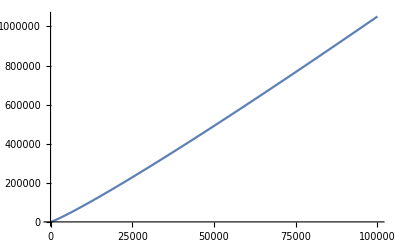

```mathematica
Plot[Log[x!],{x,0,100000}]
```

```mathematica
FactorInteger[10!]
```

{{2,8},{3,4},{5,2},{7,1}}

```mathematica
facAv[n_]:=#1/#2&@@(Total/@Transpose[{#1#2,#1+#2}&@@@FactorInteger[n!]])
{#,N@#}&/@(facAv/@Range[100])
```

{{1/2,0.5},{2/3,0.666667},{5/7,0.714286},{1,1.},{14/15,0.933333},{19/17,1.11765},{26/25,1.04},{8/7,1.14286},{19/15,1.26667},{45/32,1.40625},{14/11,1.27273},{63/47,1.34043},{76/61,1.2459},{85/63,1.34921},{93/65,1.43077},{101/69,1.46377},{118/87,1.35632},{7/5,1.4},{29/22,1.31818},{154/113,1.36283},{164/115,1.42609},{59/39,1.51282},{200/141,1.41844},{209/145,1.44138},{73/49,1.4898},{234/149,1.57047},{243/152,1.59868},{254/155,1.63871},{283/185,1.52973},{293/188,1.55851},{81/55,1.47273},{334/225,1.48444},{348/227,1.53304},{367/229,1.60262},{379/231,1.64069},{389/235,1.65532},{142/91,1.56044},{447/275,1.62545},{463/277,1.67148},{474/281,1.68683},{515/323,1.59443},{527/326,1.61656},{57/37,1.54054},{585/373,1.56836},{149/94,1.58511},{23/14,1.64286},{334/213,1.56808},{679/431,1.57541},{693/433,1.60046},{705/436,1.61697},{725/438,1.65525},{106/63,1.68254},{53/33,1.60606},{806/499,1.61523},{274/167,1.64072},{167/101,1.65347},{857/507,1.69034},{888/509,1.7446},{947/569,1.66432},{959/573,1.67365},{204/127,1.6063},{81/49,1.65306},{533/320,1.66563},{539/323,1.66873},{137/81,1.69136},{1112/651,1.70814},{1179/719,1.63978},{600/361,1.66205},{613/362,1.69337},{1240/727,1.70564},{1311/799,1.6408},{441/268,1.64552},{698/439,1.58998},{287/176,1.63068},{1448/883,1.63986},{1471/886,1.66027},{1489/888,1.6768},{137/81,1.69136},{1586/971,1.63337},{1599/976,1.63832},{1611/980,1.64388},{827/491,1.68432},{1737/1066,1.62946},{1751/1070,1.63645},{1773/1072,1.65392},{303/179,1.69274},{925/538,1.71933},{1867/1080,1.7287},{326/195,1.67179},{1969/1174,1.67717},{663/392,1.69133},{224/131,1.70992},{2050/1181,1.73582},{2099/1183,1.7743},{2123/1185,1.79156},{712/397,1.79345},{2233/1289,1.73235},{2249/1292,1.74071},{2266/1295,1.74981},{760/433,1.7552}}

```mathematica
Format[("2")^("2"),TraditionalForm]
```

2^2

```mathematica
{a, 3, b}{0,1,0}
```

{0,3,0}

```mathematica
fib[mod2_Integer][n_Integer/;n>0]/;0≤ mod2<2:=fib[mod2][n]=fib[0][n-1 + mod2]+rE[0,2]fib[1][n-1]
fib[mod2_][n_Integer/;n<0]/;0≤ mod2<2:=fib[mod2][n]=(fib[0][n+1]+rE[mod2,2]fib[1][n+1])/2
fib[mod2_][n_Integer/;n<0]/;0≤ mod2<2:=fib[mod2][n]=rE[mod2+1,2]fib[1][n+1]+rE[mod2,2](2-mod2)fib[0][n+1 ]
```

```mathematica
Fibonacci/@Range[20]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

```mathematica
ClearAll[fib]
?fib
```

Global`fib

```mathematica
ClearAll[fib]

fib[0][-1]=-1-rE[2,3];
fib[0][0]=0;
fib[1][0]=1+rE[1,3];
fib[0][1]=1+rE[2,3];
fib[1][1]=fib[1][0]+fib[0][-1];
fib[1][-1]=fib[0][1]+fib[0][0];

fib[mod2_Integer][n_Integer]/;(0≤ mod2 && mod2<2)&&n≥ 2:=fib[mod2][n]=rE[1+mod2,3]fib[mod2][n-1 ]+rE[2-mod2,3]fib[mod2+1][n-2]
fib[mod2_Integer][n_Integer]/;(0≤ mod2 && mod2<2)&&n≤ 2:=fib[mod2][n]=(fib[mod2+1][n+2]-fib[mod2+1][n+1 ])
fib[mod2_Integer][n_Integer]/;mod2<0 || mod2≥2:=fib[Mod[mod2,2]][n]
fib[][n_Integer]:=fib[0][n]+fib[1][n]
ta=Chop@N@Array[{#,{{ fib[0][#],fib[1][#],fib[][#]}}}&,20,0]
Select[ta,Element[#,Reals]&]
TableForm[{ta}]
(*ta=Array[{#,Transpose[({#,formatPrimeFactors[FactorInteger[Re[#]]]}&)/@{ fib[0][#],fib[1][#],fib[][#]}]}&,50,-10]

tap=Transpose[Transpose[{ConstantArray[#1,Length[#2]],#2}]&@@@Transpose@{ta[[All,1]],ta[[All,2,1]]}]
PlotExplorer@ListPlot[tap,ImageSize->Large,GridLines->Automatic,Joined->True,Mesh->All,PlotRange->{{10,14},{20,200}}]*)
```

{{0,{{0,0.5+0.866025 ⅈ,0.5+0.866025 ⅈ}}},{1.,{{0.5-0.866025 ⅈ,0.+1.73205 ⅈ,0.5+0.866025 ⅈ}}},{2.,{{1.,1.5-0.866025 ⅈ,2.5-0.866025 ⅈ}}},{3.,{{1.,-1.,0}}},{4.,{{-2.,0.+1.73205 ⅈ,-2.+1.73205 ⅈ}}},{5.,{{1.5-0.866025 ⅈ,1.,2.5-0.866025 ⅈ}}},{6.,{{1.5+0.866025 ⅈ,0.5-2.59808 ⅈ,2.-1.73205 ⅈ}}},{7.,{{-2.,-2.5+2.59808 ⅈ,-4.5+2.59808 ⅈ}}},{8.,{{-1.5-0.866025 ⅈ,2.+1.73205 ⅈ,0.5+0.866025 ⅈ}}},{9.,{{5.,1.5-4.33013 ⅈ,6.5-4.33013 ⅈ}}},{10.,{{-2.+1.73205 ⅈ,-3.,-5.+1.73205 ⅈ}}},{11.,{{-5.-1.73205 ⅈ,-1.+6.9282 ⅈ,-6.+5.19615 ⅈ}}},{12.,{{5.5-0.866025 ⅈ,6.-5.19615 ⅈ,11.5-6.06218 ⅈ}}},{13.,{{4.5+2.59808 ⅈ,-3.5-6.06218 ⅈ,1.-3.4641 ⅈ}}},{14.,{{-12.,-5.5+11.2583 ⅈ,-17.5+11.2583 ⅈ}}},{15.,{{2.5-4.33013 ⅈ,8.+1.73205 ⅈ,10.5-2.59808 ⅈ}}},{16.,{{15.+3.4641 ⅈ,3.5-18.1865 ⅈ,18.5-14.7224 ⅈ}}},{17.,{{-13.+3.4641 ⅈ,-15.+10.3923 ⅈ,-28.+13.8564 ⅈ}}},{18.,{{-14.-6.9282 ⅈ,6.+19.0526 ⅈ,-8.+12.1244 ⅈ}}},{19.,{{29.5-0.866025 ⅈ,17.-27.7128 ⅈ,46.5-28.5788 ⅈ}}}}

{{3.,{{1.,-1.,0}}}}

0
0
0.5+0.866025 ⅈ
0.5+0.866025 ⅈ | 1.
0.5-0.866025 ⅈ
0.+1.73205 ⅈ
0.5+0.866025 ⅈ | 2.
1.
1.5-0.866025 ⅈ
2.5-0.866025 ⅈ | 3.
1.
-1.
0 | 4.
-2.
0.+1.73205 ⅈ
-2.+1.73205 ⅈ | 5.
1.5-0.866025 ⅈ
1.
2.5-0.866025 ⅈ | 6.
1.5+0.866025 ⅈ
0.5-2.59808 ⅈ
2.-1.73205 ⅈ | 7.
-2.
-2.5+2.59808 ⅈ
-4.5+2.59808 ⅈ | 8.
-1.5-0.866025 ⅈ
2.+1.73205 ⅈ
0.5+0.866025 ⅈ | 9.
5.
1.5-4.33013 ⅈ
6.5-4.33013 ⅈ | 10.
-2.+1.73205 ⅈ
-3.
-5.+1.73205 ⅈ | 11.
-5.-1.73205 ⅈ
-1.+6.9282 ⅈ
-6.+5.19615 ⅈ | 12.
5.5-0.866025 ⅈ
6.-5.19615 ⅈ
11.5-6.06218 ⅈ | 13.
4.5+2.59808 ⅈ
-3.5-6.06218 ⅈ
1.-3.4641 ⅈ | 14.
-12.
-5.5+11.2583 ⅈ
-17.5+11.2583 ⅈ | 15.
2.5-4.33013 ⅈ
8.+1.73205 ⅈ
10.5-2.59808 ⅈ | 16.
15.+3.4641 ⅈ
3.5-18.1865 ⅈ
18.5-14.7224 ⅈ | 17.
-13.+3.4641 ⅈ
-15.+10.3923 ⅈ
-28.+13.8564 ⅈ | 18.
-14.-6.9282 ⅈ
6.+19.0526 ⅈ
-8.+12.1244 ⅈ | 19.
29.5-0.866025 ⅈ
17.-27.7128 ⅈ
46.5-28.5788 ⅈ

```mathematica
ClearAll[fibRue]
fibRue[0][-1]=-1;
fibRue[0][0]=1;
fibRue[1][0]=0;
fibRue[0][1]=2;
fibRue[1][1]=fibRue[1][0]+fibRue[0][-1];
fibRue[1][-1]=fibRue[0][1]+fibRue[0][0];

fibRue[mod2_Integer][n_Integer]/;(0≤ mod2 && mod2<2)&&n≥ 2:=fibRue[mod2][n]=fibRue[mod2][n-1 ]+rE[0,2]fibRue[mod2+1][n-2]
fibRue[mod2_Integer][n_Integer]/;(0≤ mod2 && mod2<2)&&n≤ 2:=fibRue[mod2][n]=(fibRue[mod2+1][n+2]-fibRue[mod2+1][n+1 ])
fibRue[mod2_Integer][n_Integer]/;mod2<0 || mod2≥2:=fibRue[Mod[mod2,2]][n]
fibRue[][n_Integer]:=fibRue[0][n]+fibRue[1][n]
```

```mathematica
ClearAll[a]
a[-3]=0;
a[-2]=0;
a[-1]=-1;
a[0]=1;
a[1]=rE[1,6];
a[2]=1+rE[3,6];
a[n_]:=a[n]=Chop@N[a[n-2]rE[4+n,6]+a[n-1]rE[n,6]+a[n-3]rE[2+n,6] ]
ta=Array[a,1000,0];
ReIm@*Chop/@ta[[1;;150]]
TableForm[{IntegerPart/@Select[ta,Element[#,Reals]&&#>1.5&],formatPrimeFactors@*FactorInteger@*IntegerPart/@Select[ta,Element[#,Reals]&&#>1.5&]}]
Manipulate[ListPlot[(ReIm/@ta)[[1;;i]],ImageSize->Large,GridLines->Automatic,Joined->True,Mesh->All,PlotRange->All],{i,5,100,1}]
```

$Aborted

```mathematica
|
```

```mathematica
primeFactors={#,FactorInteger[#]}&/@Range[300];
formatPrimeFactors[factors_]:=ToString[Times@@(HoldForm[#1^#2]&@@@factors),TraditionalForm]
pF2={#1,Total@#2[[All,2]],formatPrimeFactors[#2]}&@@@ primeFactors;
(*maxStrLength= Max[StringLength[StringJoin[ToString/@ Flatten[#]]]&/@primeFactors[[All,2]]]*)
pF3={#[[1]],#[[3]],StringRepeat["->",#[[2]]]<>" "<>ToString[#[[2]]]}&/@pF2;
(*pF3=PadRight[ArrayPad[{#[[1]],#[[2]]},{{#[[2]]-1,0}},"--->"]&/@pF2,Automatic,""]*)
(*pF3=MapIndexed[Transpose@Insert[ConstantArray["",{Length[pF3a]-1,Length[#1]}],#,First[#2]]&,pF3a];*)
Grid[pF3,Dividers->{False,All},Alignment->{{Right,Right,Left}}](*,TableSpacing->{2, 1},TableAlignments->{{Left,Right,Left}}]*)
```

1 | 1^1 | -> 1
2 | 2^1 | -> 1
3 | 3^1 | -> 1
4 | 2^2 | ->-> 2
5 | 5^1 | -> 1
6 | 2^1 3^1 | ->-> 2
7 | 7^1 | -> 1
8 | 2^3 | ->->-> 3
9 | 3^2 | ->-> 2
10 | 2^1 5^1 | ->-> 2
11 | 11^1 | -> 1
12 | 2^2 3^1 | ->->-> 3
13 | 13^1 | -> 1
14 | 2^1 7^1 | ->-> 2
15 | 3^1 5^1 | ->-> 2
16 | 2^4 | ->->->-> 4
17 | 17^1 | -> 1
18 | 2^1 3^2 | ->->-> 3
19 | 19^1 | -> 1
20 | 2^2 5^1 | ->->-> 3
21 | 3^1 7^1 | ->-> 2
22 | 2^1 11^1 | ->-> 2
23 | 23^1 | -> 1
24 | 2^3 3^1 | ->->->-> 4
25 | 5^2 | ->-> 2
26 | 2^1 13^1 | ->-> 2
27 | 3^3 | ->->-> 3
28 | 2^2 7^1 | ->->-> 3
29 | 29^1 | -> 1
30 | 2^1 3^1 5^1 | ->->-> 3
31 | 31^1 | -> 1
32 | 2^5 | ->->->->-> 5
33 | 3^1 11^1 | ->-> 2
34 | 2^1 17^1 | ->-> 2
35 | 5^1 7^1 | ->-> 2
36 | 2^2 3^2 | ->->->-> 4
37 | 37^1 | -> 1
38 | 2^1 19^1 | ->-> 2
39 | 3^1 13^1 | ->-> 2
40 | 2^3 5^1 | ->->->-> 4
41 | 41^1 | -> 1
42 | 2^1 3^1 7^1 | ->->-> 3
43 | 43^1 | -> 1
44 | 2^2 11^1 | ->->-> 3
45 | 3^2 5^1 | ->->-> 3
46 | 2^1 23^1 | ->-> 2
47 | 47^1 | -> 1
48 | 2^4 3^1 | ->->->->-> 5
49 | 7^2 | ->-> 2
50 | 2^1 5^2 | ->->-> 3
51 | 3^1 17^1 | ->-> 2
52 | 2^2 13^1 | ->->-> 3
53 | 53^1 | -> 1
54 | 2^1 3^3 | ->->->-> 4
55 | 5^1 11^1 | ->-> 2
56 | 2^3 7^1 | ->->->-> 4
57 | 3^1 19^1 | ->-> 2
58 | 2^1 29^1 | ->-> 2
59 | 59^1 | -> 1
60 | 2^2 3^1 5^1 | ->->->-> 4
61 | 61^1 | -> 1
62 | 2^1 31^1 | ->-> 2
63 | 3^2 7^1 | ->->-> 3
64 | 2^6 | ->->->->->-> 6
65 | 5^1 13^1 | ->-> 2
66 | 2^1 3^1 11^1 | ->->-> 3
67 | 67^1 | -> 1
68 | 2^2 17^1 | ->->-> 3
69 | 3^1 23^1 | ->-> 2
70 | 2^1 5^1 7^1 | ->->-> 3
71 | 71^1 | -> 1
72 | 2^3 3^2 | ->->->->-> 5
73 | 73^1 | -> 1
74 | 2^1 37^1 | ->-> 2
75 | 3^1 5^2 | ->->-> 3
76 | 2^2 19^1 | ->->-> 3
77 | 7^1 11^1 | ->-> 2
78 | 2^1 3^1 13^1 | ->->-> 3
79 | 79^1 | -> 1
80 | 2^4 5^1 | ->->->->-> 5
81 | 3^4 | ->->->-> 4
82 | 2^1 41^1 | ->-> 2
83 | 83^1 | -> 1
84 | 2^2 3^1 7^1 | ->->->-> 4
85 | 5^1 17^1 | ->-> 2
86 | 2^1 43^1 | ->-> 2
87 | 3^1 29^1 | ->-> 2
88 | 2^3 11^1 | ->->->-> 4
89 | 89^1 | -> 1
90 | 2^1 3^2 5^1 | ->->->-> 4
91 | 7^1 13^1 | ->-> 2
92 | 2^2 23^1 | ->->-> 3
93 | 3^1 31^1 | ->-> 2
94 | 2^1 47^1 | ->-> 2
95 | 5^1 19^1 | ->-> 2
96 | 2^5 3^1 | ->->->->->-> 6
97 | 97^1 | -> 1
98 | 2^1 7^2 | ->->-> 3
99 | 3^2 11^1 | ->->-> 3
100 | 2^2 5^2 | ->->->-> 4
101 | 101^1 | -> 1
102 | 2^1 3^1 17^1 | ->->-> 3
103 | 103^1 | -> 1
104 | 2^3 13^1 | ->->->-> 4
105 | 3^1 5^1 7^1 | ->->-> 3
106 | 2^1 53^1 | ->-> 2
107 | 107^1 | -> 1
108 | 2^2 3^3 | ->->->->-> 5
109 | 109^1 | -> 1
110 | 2^1 5^1 11^1 | ->->-> 3
111 | 3^1 37^1 | ->-> 2
112 | 2^4 7^1 | ->->->->-> 5
113 | 113^1 | -> 1
114 | 2^1 3^1 19^1 | ->->-> 3
115 | 5^1 23^1 | ->-> 2
116 | 2^2 29^1 | ->->-> 3
117 | 3^2 13^1 | ->->-> 3
118 | 2^1 59^1 | ->-> 2
119 | 7^1 17^1 | ->-> 2
120 | 2^3 3^1 5^1 | ->->->->-> 5
121 | 11^2 | ->-> 2
122 | 2^1 61^1 | ->-> 2
123 | 3^1 41^1 | ->-> 2
124 | 2^2 31^1 | ->->-> 3
125 | 5^3 | ->->-> 3
126 | 2^1 3^2 7^1 | ->->->-> 4
127 | 127^1 | -> 1
128 | 2^7 | ->->->->->->-> 7
129 | 3^1 43^1 | ->-> 2
130 | 2^1 5^1 13^1 | ->->-> 3
131 | 131^1 | -> 1
132 | 2^2 3^1 11^1 | ->->->-> 4
133 | 7^1 19^1 | ->-> 2
134 | 2^1 67^1 | ->-> 2
135 | 3^3 5^1 | ->->->-> 4
136 | 2^3 17^1 | ->->->-> 4
137 | 137^1 | -> 1
138 | 2^1 3^1 23^1 | ->->-> 3
139 | 139^1 | -> 1
140 | 2^2 5^1 7^1 | ->->->-> 4
141 | 3^1 47^1 | ->-> 2
142 | 2^1 71^1 | ->-> 2
143 | 11^1 13^1 | ->-> 2
144 | 2^4 3^2 | ->->->->->-> 6
145 | 5^1 29^1 | ->-> 2
146 | 2^1 73^1 | ->-> 2
147 | 3^1 7^2 | ->->-> 3
148 | 2^2 37^1 | ->->-> 3
149 | 149^1 | -> 1
150 | 2^1 3^1 5^2 | ->->->-> 4
151 | 151^1 | -> 1
152 | 2^3 19^1 | ->->->-> 4
153 | 3^2 17^1 | ->->-> 3
154 | 2^1 7^1 11^1 | ->->-> 3
155 | 5^1 31^1 | ->-> 2
156 | 2^2 3^1 13^1 | ->->->-> 4
157 | 157^1 | -> 1
158 | 2^1 79^1 | ->-> 2
159 | 3^1 53^1 | ->-> 2
160 | 2^5 5^1 | ->->->->->-> 6
161 | 7^1 23^1 | ->-> 2
162 | 2^1 3^4 | ->->->->-> 5
163 | 163^1 | -> 1
164 | 2^2 41^1 | ->->-> 3
165 | 3^1 5^1 11^1 | ->->-> 3
166 | 2^1 83^1 | ->-> 2
167 | 167^1 | -> 1
168 | 2^3 3^1 7^1 | ->->->->-> 5
169 | 13^2 | ->-> 2
170 | 2^1 5^1 17^1 | ->->-> 3
171 | 3^2 19^1 | ->->-> 3
172 | 2^2 43^1 | ->->-> 3
173 | 173^1 | -> 1
174 | 2^1 3^1 29^1 | ->->-> 3
175 | 5^2 7^1 | ->->-> 3
176 | 2^4 11^1 | ->->->->-> 5
177 | 3^1 59^1 | ->-> 2
178 | 2^1 89^1 | ->-> 2
179 | 179^1 | -> 1
180 | 2^2 3^2 5^1 | ->->->->-> 5
181 | 181^1 | -> 1
182 | 2^1 7^1 13^1 | ->->-> 3
183 | 3^1 61^1 | ->-> 2
184 | 2^3 23^1 | ->->->-> 4
185 | 5^1 37^1 | ->-> 2
186 | 2^1 3^1 31^1 | ->->-> 3
187 | 11^1 17^1 | ->-> 2
188 | 2^2 47^1 | ->->-> 3
189 | 3^3 7^1 | ->->->-> 4
190 | 2^1 5^1 19^1 | ->->-> 3
191 | 191^1 | -> 1
192 | 2^6 3^1 | ->->->->->->-> 7
193 | 193^1 | -> 1
194 | 2^1 97^1 | ->-> 2
195 | 3^1 5^1 13^1 | ->->-> 3
196 | 2^2 7^2 | ->->->-> 4
197 | 197^1 | -> 1
198 | 2^1 3^2 11^1 | ->->->-> 4
199 | 199^1 | -> 1
200 | 2^3 5^2 | ->->->->-> 5
201 | 3^1 67^1 | ->-> 2
202 | 2^1 101^1 | ->-> 2
203 | 7^1 29^1 | ->-> 2
204 | 2^2 3^1 17^1 | ->->->-> 4
205 | 5^1 41^1 | ->-> 2
206 | 2^1 103^1 | ->-> 2
207 | 3^2 23^1 | ->->-> 3
208 | 2^4 13^1 | ->->->->-> 5
209 | 11^1 19^1 | ->-> 2
210 | 2^1 3^1 5^1 7^1 | ->->->-> 4
211 | 211^1 | -> 1
212 | 2^2 53^1 | ->->-> 3
213 | 3^1 71^1 | ->-> 2
214 | 2^1 107^1 | ->-> 2
215 | 5^1 43^1 | ->-> 2
216 | 2^3 3^3 | ->->->->->-> 6
217 | 7^1 31^1 | ->-> 2
218 | 2^1 109^1 | ->-> 2
219 | 3^1 73^1 | ->-> 2
220 | 2^2 5^1 11^1 | ->->->-> 4
221 | 13^1 17^1 | ->-> 2
222 | 2^1 3^1 37^1 | ->->-> 3
223 | 223^1 | -> 1
224 | 2^5 7^1 | ->->->->->-> 6
225 | 3^2 5^2 | ->->->-> 4
226 | 2^1 113^1 | ->-> 2
227 | 227^1 | -> 1
228 | 2^2 3^1 19^1 | ->->->-> 4
229 | 229^1 | -> 1
230 | 2^1 5^1 23^1 | ->->-> 3
231 | 3^1 7^1 11^1 | ->->-> 3
232 | 2^3 29^1 | ->->->-> 4
233 | 233^1 | -> 1
234 | 2^1 3^2 13^1 | ->->->-> 4
235 | 5^1 47^1 | ->-> 2
236 | 2^2 59^1 | ->->-> 3
237 | 3^1 79^1 | ->-> 2
238 | 2^1 7^1 17^1 | ->->-> 3
239 | 239^1 | -> 1
240 | 2^4 3^1 5^1 | ->->->->->-> 6
241 | 241^1 | -> 1
242 | 2^1 11^2 | ->->-> 3
243 | 3^5 | ->->->->-> 5
244 | 2^2 61^1 | ->->-> 3
245 | 5^1 7^2 | ->->-> 3
246 | 2^1 3^1 41^1 | ->->-> 3
247 | 13^1 19^1 | ->-> 2
248 | 2^3 31^1 | ->->->-> 4
249 | 3^1 83^1 | ->-> 2
250 | 2^1 5^3 | ->->->-> 4
251 | 251^1 | -> 1
252 | 2^2 3^2 7^1 | ->->->->-> 5
253 | 11^1 23^1 | ->-> 2
254 | 2^1 127^1 | ->-> 2
255 | 3^1 5^1 17^1 | ->->-> 3
256 | 2^8 | ->->->->->->->-> 8
257 | 257^1 | -> 1
258 | 2^1 3^1 43^1 | ->->-> 3
259 | 7^1 37^1 | ->-> 2
260 | 2^2 5^1 13^1 | ->->->-> 4
261 | 3^2 29^1 | ->->-> 3
262 | 2^1 131^1 | ->-> 2
263 | 263^1 | -> 1
264 | 2^3 3^1 11^1 | ->->->->-> 5
265 | 5^1 53^1 | ->-> 2
266 | 2^1 7^1 19^1 | ->->-> 3
267 | 3^1 89^1 | ->-> 2
268 | 2^2 67^1 | ->->-> 3
269 | 269^1 | -> 1
270 | 2^1 3^3 5^1 | ->->->->-> 5
271 | 271^1 | -> 1
272 | 2^4 17^1 | ->->->->-> 5
273 | 3^1 7^1 13^1 | ->->-> 3
274 | 2^1 137^1 | ->-> 2
275 | 5^2 11^1 | ->->-> 3
276 | 2^2 3^1 23^1 | ->->->-> 4
277 | 277^1 | -> 1
278 | 2^1 139^1 | ->-> 2
279 | 3^2 31^1 | ->->-> 3
280 | 2^3 5^1 7^1 | ->->->->-> 5
281 | 281^1 | -> 1
282 | 2^1 3^1 47^1 | ->->-> 3
283 | 283^1 | -> 1
284 | 2^2 71^1 | ->->-> 3
285 | 3^1 5^1 19^1 | ->->-> 3
286 | 2^1 11^1 13^1 | ->->-> 3
287 | 7^1 41^1 | ->-> 2
288 | 2^5 3^2 | ->->->->->->-> 7
289 | 17^2 | ->-> 2
290 | 2^1 5^1 29^1 | ->->-> 3
291 | 3^1 97^1 | ->-> 2
292 | 2^2 73^1 | ->->-> 3
293 | 293^1 | -> 1
294 | 2^1 3^1 7^2 | ->->->-> 4
295 | 5^1 59^1 | ->-> 2
296 | 2^3 37^1 | ->->->-> 4
297 | 3^3 11^1 | ->->->-> 4
298 | 2^1 149^1 | ->-> 2
299 | 13^1 23^1 | ->-> 2
300 | 2^2 3^1 5^2 | ->->->->-> 5

```mathematica
2^2
3^1
2^3
3^2
2^(2^2)
3^(3^3)
```

4

3

8

9

16

7625597484987

```mathematica
Tetration
```

```mathematica
rootsOfUnity[n_]:=Table[ruE[k,n], {k,0,n-1}]
unityRootSum[coeffs_]:=coeffs . rootsOfUnity[Length[coeffs]]
unityRootCoeffs[sum_,n_]:=Table[{ruE[k,n],Coefficient[sum,Exp[(2 Pi I)/n],k]},{k,0,n-1}] 
expandUnityRootEq[n_:3]:=Product[Sum[Symbol["x" <>ToString[i]<>ToString[j]]ruE[i-1,n],{i,1,n}],{j,1,n}]
```

```mathematica
GatherBy[List@@@List@@Expand[expandUnityRootEq[]], If[Length[#]==3, 1, First[#]]&]
```

```mathematica
expandUnityRootEq[]//ExpandAll
Coefficient[expandUnityRootEq[],ⅇ^((2 ⅈ π)/3),1]
unityRootCoeffs[ expandUnityRootEq[], 3]//TableForm
```

```mathematica
sum1[n_]:=Times@@(Sum[Symbol["s"<>ToString[i]],{i,1,#}] + x &/@Range[n])
```

```mathematica
sum1[3]
```

```mathematica
(s1+x) (s1+s2 -s3+x) (s1+s2+s3+x)
{x^#&/@Range[0,3],CoefficientList[Expand[(s1+x) (s1+s2 -s3+x) (s1+s2+s3+x)],x]}//Transpose//TableForm
```

```mathematica
{x^#&/@Range[0,3],CoefficientList[Expand[sum1[3]],x]}//Transpose//TableForm
```

```mathematica
u''''[x]=0
```

```mathematica
D[p'[x]*u'[x],{x,11}]
```

```mathematica
c1[n_,i_]:=(n-1)!/((n-i)! (i-1)!)
```

```mathematica
c1[#,Range[#]]&/@Range[12]
```

```mathematica
efsns=TableForm[{#1,#2,FullSimplify[MonomialList[#2]]}&@@@fsns]
```

```mathematica
Select[efsns, Length[#3]<6&]
```

```mathematica
(x-Subscript[s, 1]) (x+Subscript[s, 1]) (x+ⅇ^(-(ⅈ π)/3) Subscript[s, 1]) (x+ⅇ^((ⅈ π)/3) Subscript[s, 1]) (x+ⅇ^(-(2 ⅈ π)/3) Subscript[s, 1]) (x+ⅇ^((2 ⅈ π)/3) Subscript[s, 1])//Expand//FullSimplify
```

```mathematica
polyFromRootsFn[n_,rootFn_:(Subscript[s, #]&),xFn_:(x&)]:=Product[(xFn[i] + rootFn[i]),{i,1,n}]
allUnityPolys[n_]:={#,polyFromRootsFn[n, Function[{x},s ruE[#[[x]],2n]]]}&/@DeleteDuplicates[Sort/@Tuples[Range[0,2n-1],n]]
```

```mathematica
{#1,#2,FullSimplify[MonomialList[#2]]}&@@@allUnityPolys[3]//TableForm
```

```mathematica
polyFromRootsFn[3]
```

```mathematica
List[Sum[{i,j,k},{i,0,2},{j,i,2},{k,i+j,2}]]
DeleteDuplicates[Sort/@Tuples[Range[0,2],3]]
```

```mathematica
a[m_,n_]:=m^2-n^2
b[m_,n_]:=2m n
c[m_,n_]:=m^2+n^2
r[m_,n_]:={a[m,n],b[m,n],c[m,n]}
Table[{{a,b,c},r[m,n],r[m,n]^2},{m,-3,3},{n,-3,3}]//MatrixForm
Plot3D[a[m,n],{m,-10,10},{n,-10,10}]
```

```mathematica
Subscript[mod, i_,j_][n_]:=Mod[n, Prime[i]^j]
Subscript[stylizedMod, i_,j_][n_]:=With[{primeij= Prime[i]^j,modN=Mod[n, Prime[i]^j]},
Which[
modN ==0,Style[ToString[0],Red],
modN < n,Style[ToString[modN]<>"%" <>ToString[Prime[i]^j],Larger,Bold],
modN==n,Style[ToString[modN],Smaller]]]
modMatrix[n_]:=Table[Subscript[stylizedMod, i,j][n],{i,1, PrimePi[n]+1},{j,1, Log2[n]+1}]
```

```mathematica
modMatrix[5]
```

```mathematica
modMatrixFormWHeadings[mat_]:=With[{rowHeader=Prime/@Range[Length[mat]],colHeader=("p")^#&/@Range[0,Length[First[mat]]]},
MatrixForm[mat,TableAlignments->Right,TableHeadings->{rowHeader,colHeader}]]
```

```mathematica
modMatrixFormWHeadings[modMatrix[#]]&/@ (3^#&/@Range[5])//TableForm
```

```mathematica
{#,modMatrixFormWHeadings[modMatrix[#]]}&/@Range[2,50]//TableForm
```

```mathematica
rotatePoly[poly_,k_,n_]:=poly /. x->ruE[k,n]x
```

```mathematica
p1=polyFromRoots[s1,s2,s3] + ruE[2,3]Sum[rotatePoly[polyFromRoots[s1,s2,s3],k,3],{k,1,2}]//Expand
Collect[p1,x]
```

```mathematica
ruE[2,3]rotatePoly[polyFromRoots[s1,s2 ,s3],1,3]+ruE[1,3]rotatePoly[polyFromRoots[s1,s2 ,s3],2,3]/.x->s1//Expand//FullSimplify
```

```mathematica
Remove["s"]
```

```mathematica
Subscript[sN, s_,e_]=Range[s,e];
Subscript[sN, e_]=Range[e];
```

```mathematica
polyCoeffEqOfRoots[roots_List]:={Subscript[c, Length[roots]-#],Plus@@Times@@@Subsets[roots,{#}]}&/@Range[Length[roots]]
polyCoeffEqOfRoots[n_:3,sym_:s]:=polyCoeffEqOfRoots[(Subscript[s, #]&/@Subscript[sN, n])];
polyCoeffEqOfRoots[roots__]:=polyCoeffEqOfRoots[{roots}]
```

```mathematica
symmetricTransform[sym_,n_]:=Subscript[s, i_]->Subscript[t, 1]+ruE[i, n] Subscript[t, 2] +ruE[n-1-2i,2n] Subscript[t, 3]
Collect[polyCoeffEqOfRoots[]/.symmetricTransform[s,3]//Expand//FullSimplify,{Subscript[t, 1],Subscript[t, 2],Subscript[t, 3]}]
TableForm[%]
```

```mathematica
ruE[1,6]+ruE[5,6]+1//FullSimplify
```

```mathematica
symmetricTransform[sym_,n_]:=Subscript[s, i_]->Subscript[t, 1]+ruE[k1, n] Subscript[t, 2] +ruE[n-i,n] Subscript[t, 3]
Collect[polyCoeffEqOfRoots[]/.symmetricTransform[s,3]//Expand//FullSimplify,{Subscript[t, 1],Subscript[t, 2],Subscript[t, 3]}]
TableForm[%]
```

```mathematica
splitPower[var1_,var2_,n_]:=Product[(var1 +ruE[i,n]var2),{i,0,n-1}]
```

```mathematica
splitPower[Subscript[t, 1],Subscript[t, 2],3]//Expand//FullSimplify
```

```mathematica
Remove["indexCoeffProd*"]
indexCoeffProd[n_,coeffVar_:e,var1_:a,var2_:b]:= Product[a Subscript[e, 1,i]+b Subscript[e, 2,i],{i,1,n}]
Subscript[indexCoeffProd1, n_,sym_:e][n1s_]/;SubsetQ[Subscript[sN, n],n1s]:=Product[Subscript[sym, 1,k],{k,n1s}]Product[Subscript[sym, 2,k],{k,Complement[Subscript[sN, n],n1s]}]
indexCoeffProdAll[n_,sym_:e]:=Subscript[indexCoeffProd1, n,sym]/@Subsets[Subscript[sN, n]]
Subscript[indexCoeffProd1, 3][ {1,2}]
indexCoeffProdAll[3]
```

```mathematica
indexCoeffProdAll[3]/.Subscript[e, i_,j_]->Subscript[a, i] Subscript[e, i,j] /.{Subscript[a, 1]->a,Subscript[a, 2]->b}//Total
indexCoeffProd[3]//Expand
```

```mathematica
rGen[d_]:=(1+ruE[1,3](1+d) + ruE[2,3](1/d))
rGenRotPow[_,0]=1
rGenRotPow[form_,pow_]:=
l1={Expand[#],ComplexExpand[#]}& @*(rGen[2,#]&)/@Range[10];
TableForm[l1]
```

```mathematica
subsetsUnitySum[size_:1,sym_:c]:=Subsets[(#1+ruE[1,3]#2+ruE[2,3]#3)&@@@Permutations[{Subscript[sym, 0],Subscript[sym, 1],Subscript[sym, 2]}],{size}]
```

```mathematica
Flatten[subsetsUnitySum[]]^2//Expand
```